## R0 calculations

First, I want to see how changing our different components of our expression would change the expected R0

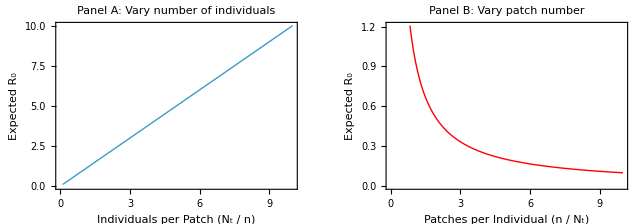

```mathematica
(* RESET AND DEFINE *)
ClearAll[initialInfected, ntRange, nRange, r0Formula, r0DensityData1, r0DensityData2]
initialInfected = 1;

(* Define fixed quantities *)
fixedN = 1000;
fixedNt = 1000;

(* FULL EXPRESSION *)
r0Formula[nt_, n_] := n * (1/n)^2 * (nt - initialInfected)  (* Equivalent to (nt - 1)/n *)

(* PANEL A: Vary Nt, fix n — plot vs. individuals per patch *)
ntRange = Range[100, 10000, 50];
r0DensityData1 = Table[
  {nt/fixedN, r0Formula[nt, fixedN]},   (* x = density *)
  {nt, ntRange}
];

(* PANEL B: Vary n, fix Nt — plot vs. patches per individual *)
nRange = Range[100, 10000, 50];
r0DensityData2 = Table[
  {n/fixedNt, r0Formula[fixedNt, n]},   (* x = inverse density *)
  {n, nRange}
];

(* PANEL A PLOT *)
panelA = ListLinePlot[
  r0DensityData1,
  Frame -> True,
  FrameLabel -> {
    Style["Individuals per Patch (Nₜ / n)", 14],
    Style["Expected R₀", 14]
  },
  PlotLabel -> 
    Style["Panel A: Vary number of individuals", 14, Bold],
  PlotStyle -> Thick,
  ImageSize -> 400
];

(* PANEL B PLOT *)
panelB = ListLinePlot[
  r0DensityData2,
  Frame -> True,
  FrameLabel -> {
    Style["Patches per Individual (n / Nₜ)", 14],
    Style["Expected R₀", 14]
  },
  PlotLabel -> 
    Style["Panel B: Vary patch number", 14, Bold],
  PlotStyle -> {Thick, Red},
  ImageSize -> 400
];

(* COMBINE PLOTS *)
GraphicsRow[{panelA, panelB}, Spacings -> 20]
```

```mathematica
(* PARAMETERS *)
ClearAll[weights, output, numPatches, numReps]
numPatches = 1000;
initialInfected = 1;
totalIndividuals = 1251;
numReps = 1000;

weights = ConstantArray[1/numPatches, numPatches];

(* Expected R0 under constant patch weights *)
expectedR0 = N[numPatches * (1/numPatches)^2 * (totalIndividuals - initialInfected)];
Print["R0 = ", expectedR0];
Print["Num patches = ", Length[weights]]
Print["Num sims = ", numReps]

(* SHARED VARIABLE FOR PARALLEL OUTPUT *)
progress = 0;
SetSharedVariable[progress];

output = ParallelTable[
    Module[{t = 0, NI = initialInfected, NT = totalIndividuals, simHistory = {}, Sloc, Iloc, cloc},
      While[NI > 0,
        Sloc = RandomChoice[weights -> Range[1, numPatches], NT - NI];
        Iloc = RandomChoice[weights -> Range[1, numPatches], NI];
        cloc = Intersection[Sloc, Iloc];
        NI = Total[Count[Sloc, #] & /@ cloc];
        AppendTo[simHistory, {t++, NI, NT - NI}];
      ];
      simHistory
    ],
    {i, 1, numReps}
  ];

(* PLOTTING *)

(* 1. Extract extinction times (last timepoint in each sim) *)
extinctionTimes = Table[Last[output[[i]]][[1]], {i, numReps}];

(* 2. Infection trajectories *)
ListLinePlot[
  Table[output[[i]][[All, 2]], {i, 1, numReps}],
  PlotStyle -> Directive[Opacity[0.1]],
  ImageSize -> Large,
  Frame -> True,
  FrameStyle -> 16,
  FrameLabel -> {"Time", "Number of Infected (dies after 1 step)"},
  PlotRange -> {{0, 120}, {0, 65}}
]

(* 3. Histogram of extinction times *)
Histogram[
  extinctionTimes,
  Frame -> True,
  FrameStyle -> 16,
  PlotLabel -> Style["Extinction Time for R₀ = 1.0", 14, Bold],
  FrameLabel -> {"Time until I = 0", "Counts"}
]
```

R0 = 1.25

Num patches = 1000

Num sims = 1000

$Aborted

Part::partd: Part specification output⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification output⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification output⟦1⟧ is longer than depth of object.

Part::partd: Part specification output⟦1⟧⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification output⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification 1.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 2.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 3.⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

### Setting up some simulations to look at how changing R0 will change the results. Goal is to:

#### 1. Loop over R0 ∈ {0.8,1.0,…,2.6} 2. For each R0R0​, compute: extinction time per run mean & variance of infected counts over time max proportion infected epidemic size duration above threshold (e.g. It>10It​>10) 3. Aggregate summary statistics across 1000 simulations

```mathematica
(* PARAMETERS *)
ClearAll["Global`*"]
SeedRandom[123];

numPatches = 1000;
initialInfected = 1;
r0Values = Range[0.8, 2.6, 0.2];
numReps = 1000;
maxTime = 1000;
threshold = 100; (*This is a threshold counter to see for how long each sim stays above this number of indI*)
weights = ConstantArray[1/numPatches, numPatches];

(* FUNCTION TO RUN A SINGLE SIMULATION *)
simulateRun[totalIndividuals_] := Module[
  {t = 0, NI = initialInfected, NT = totalIndividuals, infectedHistory = {}, Sloc, Iloc, cloc, infectedEver = <||>},

  While[NI > 0 && t < maxTime,
    Sloc = RandomChoice[weights -> Range[1, numPatches], NT - NI];
    Iloc = RandomChoice[weights -> Range[1, numPatches], NI];
    cloc = Intersection[Sloc, Iloc];

    NI = Total[Count[Sloc, #] & /@ cloc];
    infectedHistory = Append[infectedHistory, NI];
    t++
  ];

  <|
    "ExtinctionTime" -> t,
    "InfectedTimeSeries" -> infectedHistory,
    "MaxProportionInfected" -> Max[infectedHistory]/totalIndividuals,
    "EpidemicSize" -> Total[infectedHistory],
    "DurationAboveThreshold" -> Count[infectedHistory, x_ /; x > threshold]
  |>
]

(* MAIN LOOP OVER R0 VALUES *)
simulationResults = Association[];

Do[
  Module[{Nt, counter = 0, progress, results, extinctionTimes, timeSeriesList, 
  propMax, sizes, durations, aligned, meanOverTime, varOverTime},
    
    Nt = Round[r0 * numPatches + initialInfected];

    Print["Running simulations for R₀ = ", r0, " (Nt = ", Nt, ")..."];

    (* Shared progress counter *)
    SetSharedVariable[counter];

    results = Monitor[
      ParallelTable[
        Module[{out = simulateRun[Nt]},
          counter++;
          out
        ],
        {numReps}
      ],
      Row[{
        "Progress: ", counter, "/", numReps, " (", 
        Round[100.0*counter/numReps], "%)"
      }]
    ];

    (* Extract summary data *)
    extinctionTimes = results[[All, "ExtinctionTime"]];
    timeSeriesList = results[[All, "InfectedTimeSeries"]];
    propMax = results[[All, "MaxProportionInfected"]];
    sizes = results[[All, "EpidemicSize"]];
    durations = results[[All, "DurationAboveThreshold"]];

    (* Align time series and compute mean/variance *)
    maxLen = Min[maxTime, Max[Length /@ timeSeriesList]];
    aligned = Transpose[PadRight[#, maxLen, 0] & /@ timeSeriesList];
    meanOverTime = Mean /@ aligned;
    varOverTime = Variance /@ aligned;

    simulationResults[r0] = <|
      "ExtinctionTimes" -> extinctionTimes,
      "MeanInfectedOverTime" -> meanOverTime,
      "VarianceInfectedOverTime" -> varOverTime,
      "MaxProportionInfected" -> propMax,
      "EpidemicSizes" -> sizes,
      "DurationsAboveThreshold" -> durations,
      "ExtinctionProbability" -> Count[extinctionTimes, t_ /; t < maxTime]/numReps
    |>;
  ],
  {r0, r0Values}
];
```

Running simulations for R₀ = 0.8 (Nt = 801)...

Running simulations for R₀ = 1. (Nt = 1001)...

Running simulations for R₀ = 1.2 (Nt = 1201)...

Running simulations for R₀ = 1.4 (Nt = 1401)...

Running simulations for R₀ = 1.6 (Nt = 1601)...

Running simulations for R₀ = 1.8 (Nt = 1801)...

Running simulations for R₀ = 2. (Nt = 2001)...

Running simulations for R₀ = 2.2 (Nt = 2201)...

Running simulations for R₀ = 2.4 (Nt = 2401)...

Running simulations for R₀ = 2.6 (Nt = 2601)...

```mathematica
CI95[data_] := Quantile[data, {0.025, 0.975}];

summarizeR0[r_] := Module[
  {
    ext = simulationResults[r]["ExtinctionTimes"],
    epi = simulationResults[r]["EpidemicSizes"],
    dur = simulationResults[r]["DurationsAboveThreshold"],
    extCI, epiCI, durCI
  },
  
  extCI = CI95[ext];
  epiCI = CI95[epi];
  durCI = CI95[dur];
  
  With[{round = Round[#, 0.01] &},  (* round to 2 decimal places *)
    {
      r,
      round@Mean[ext], round@extCI[[1]], round@extCI[[2]],
      round@Mean[epi], round@epiCI[[1]], round@epiCI[[2]],
      round@Mean[dur], round@durCI[[1]], round@durCI[[2]]
    }
  ]
];

summaryData = Prepend[
  summarizeR0 /@ r0Values,
  {
    "R₀",
    "Time to I=0", "I=0 CI Low", "I=0 CI High",
    "Mean Size", "CI Low", "CI High",
    "Mean Duration", "CI Low", "CI High"
  }
];
Grid[
  summaryData,
  Frame -> All,
  Alignment -> Center,
  Background -> {None, {LightGray, {}}},
  ItemStyle -> Directive[FontFamily -> "Helvetica", 12]
]
```

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[r0Values,{R₀,Time to I=0,I=0 CI Low,I=0 CI High,Mean Size,CI Low,CI High,Mean Duration,CI Low,CI High}].

Grid[Prepend[r0Values,{R₀,Time to I=0,I=0 CI Low,I=0 CI High,Mean Size,CI Low,CI High,Mean Duration,CI Low,CI High}],Frame→All,Alignment→Center,Background→{None,{GrayLevel[0.85],{}}},ItemStyle→Directive[FontFamily→Helvetica,12]]

#### Plot the mean time I = 0 (with 95% CI’s)

```mathematica
(* Helper for confidence intervals *)
CI95[data_] := Quantile[data, {0.025, 0.975}];

(* Mean extinction time + 95% CI *)
extinctionStatsAssoc = Table[
  Module[{vals = simulationResults[r]["ExtinctionTimes"], ci},
    ci = CI95[vals];
    <|
      "R0" -> r,
      "MeanTime" -> N[Mean[vals]],
      "CI_Lower" -> N[ci[[1]]],
      "CI_Upper" -> N[ci[[2]]]
    |>
  ],
  {r, r0Values}
];
extinctionStatsAssoc

(*(* Colour pallette *)
colorFunc = ColorData["Temperature"];
meanTimes = extinctionStatsAssoc[[All, "MeanTime"]];
minVal = Min[meanTimes];
maxVal = Max[meanTimes];
(* Normalize mean time to [0,1] for color mapping *)
normalize[val_] := (val - minVal)/(maxVal - minVal)


coloredPoints = Table[
  {
    colorFunc[normalize[stat["MeanTime"]]],
    PointSize[Medium],
    Point[{stat["R0"], stat["MeanTime"]}],
    (* vertical error bar *)
    Gray,
    Line[{
      {stat["R0"], stat["CI_Lower"]},
      {stat["R0"], stat["CI_Upper"]}
    }]
  },
  {stat, extinctionStatsAssoc}
]

Graphics[
  coloredPoints /. PointSize[_] :> PointSize[Large],
  Frame -> True,
  FrameLabel -> {
    Style["R₀", 14],
    Style["Mean Time to I=0", 14]
  },
  PlotRange -> {{0.75, 2.65}, Automatic},  
  AspectRatio -> 0.5,                     
  ImageSize -> Large,
  FrameTicks -> Automatic,
  GridLines -> None
]*)
```

Table::iterb: Iterator {r,r0Values} does not have appropriate bounds.

Table[Module[{vals=simulationResults[r][ExtinctionTimes],ci},ci=CI95[vals];Association[R0→r,MeanTime→N[Mean[vals]],CI_Lower→N[ci⟦1⟧],CI_Upper→N[ci⟦2⟧]]],{r,r0Values}]

#### Plot mean and CI epidemic sizes

{{RGBColor[0.405188, 0.204349, 0.343389],PointSize[Medium],Point[{0.8,0.00154557}],GrayLevel[0.5],Line[{{0.8,0.},{0.8,0.00749064}}]},{RGBColor[0.41013165360264336, 0.20472893446197718, 0.3437209498545647],PointSize[Medium],Point[{1.,0.0029001}],GrayLevel[0.5],Line[{{1.,0.},{1.,0.01998}}]},{RGBColor[0.5848496275413837, 0.21909568148235217, 0.3565467385876576],PointSize[Medium],Point[{1.2,0.0508976}],GrayLevel[0.5],Line[{{1.2,0.},{1.2,0.167361}}]},{RGBColor[0.7730493744883217, 0.3136864320659444, 0.45194098771400126],PointSize[Medium],Point[{1.4,0.115826}],GrayLevel[0.5],Line[{{1.4,0.},{1.4,0.242684}}]},{RGBColor[0.8310764426802314, 0.5065485307747168, 0.6366237191993249],PointSize[Medium],Point[{1.6,0.184844}],GrayLevel[0.5],Line[{{1.6,0.},{1.6,0.293567}}]},{RGBColor[0.764819803310644, 0.6424074563543393, 0.7799465263783234],PointSize[Medium],Point[{1.8,0.242963}],GrayLevel[0.5],Line[{{1.8,0.},{1.8,0.335369}}]},{RGBColor[0.6958754650988991, 0.7302766714413461, 0.8606711547919346],PointSize[Medium],Point[{2.,0.290625}],GrayLevel[0.5],Line[{{2.,0.},{2.,0.366317}}]},{RGBColor[0.6789905244955493, 0.8057123545778285, 0.8971667531251799],PointSize[Medium],Point[{2.2,0.326224}],GrayLevel[0.5],Line[{{2.2,0.},{2.2,0.392095}}]},{RGBColor[0.6667150320703114, 0.8505158704703555, 0.8965233174601511],PointSize[Medium],Point[{2.4,0.360993}],GrayLevel[0.5],Line[{{2.4,0.},{2.4,0.410246}}]},{RGBColor[0.659388, 0.872053, 0.882048],PointSize[Medium],Point[{2.6,0.386356}],GrayLevel[0.5],Line[{{2.6,0.},{2.6,0.427143}}]}}

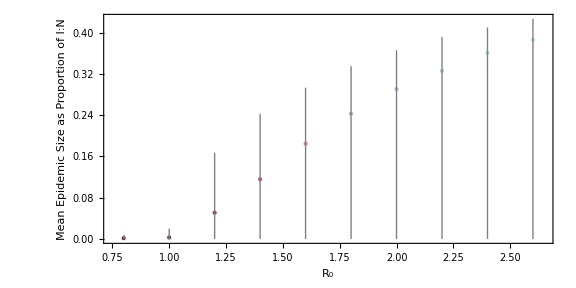

```mathematica
(* Helper for confidence intervals *)
CI95[data_] := Quantile[data, {0.025, 0.975}];

(* Epidemic size stats with 95% CI *)
MaxProportionInfectedStatsAssoc = Table[
  Module[{vals = simulationResults[r]["MaxProportionInfected"], ci},
    ci = CI95[vals];
    <|
      "R0" -> r,
      "MeanSize" -> N[Mean[vals]],
      "CI_Lower" -> N[ci[[1]]],
      "CI_Upper" -> N[ci[[2]]]
    |>
  ],
  {r, r0Values}
];
(* Colour palette *)
colorFunc = ColorData["CandyColors"];
meanSizes = MaxProportionInfectedStatsAssoc[[All, "MeanSize"]];
minSize = Min[meanSizes];
maxSize = Max[meanSizes];
normalizeSize[val_] := (val - minSize)/(maxSize - minSize);

(* Generate graphics elements *)
coloredSizePoints = Table[
  {
    colorFunc[normalizeSize[stat["MeanSize"]]],
    PointSize[Medium],
    Point[{stat["R0"], stat["MeanSize"]}],
    (* vertical error bar *)
    Gray,
    Line[{
      {stat["R0"], stat["CI_Lower"]},
      {stat["R0"], stat["CI_Upper"]}
    }]
  },
  {stat, MaxProportionInfectedStatsAssoc}
]
Graphics[
  coloredSizePoints /. PointSize[_] :> PointSize[Large],
  Frame -> True,
  FrameLabel -> {
    Style["R₀", 14],
    Style["Mean Epidemic Size as Proportion of I:N", 14]
  },
  PlotRange -> {{0.75, 2.65}, Automatic},
  AspectRatio -> 0.5,
  ImageSize -> Large,
  FrameTicks -> Automatic,
  GridLines -> None
]
```

#### What do the distributions of the values actually look like?

{1000,1000,2,1000,1000,1000,3,1000,2,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,4,1000,3,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,7,1000,1000,1000,1000,1000,1000,1000,1000,7,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,3,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,2,1000,1000,1000,3,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,5,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,3,1000,1000,1000,2,1000,1000,1000,1000,1000,4,1000,1000,1000,1000,3,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,2,1000,2,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,4,1000,1000,1000,7,1000,1000,1000,1000,1000,3,1000,7,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,6,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,3,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,1000,1000,1000,1000,1000,1000,5,1000,1000,1000,1000,1000,3,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,4,1000,1000,1000,1000,1000,1000,4,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,4,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,4,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,2,1000,1000,3,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,4,2,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,2,2,1000,3,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,2,3,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,7,2,1000,1000,2,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000}

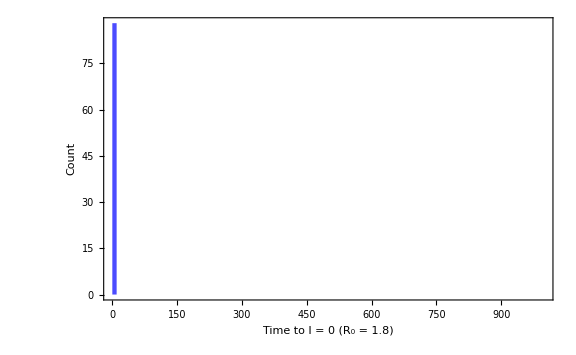

```mathematica
r = 1.8;
vals = simulationResults[r]["ExtinctionTimes"];
vals = Select[vals, # > 1 &]
Histogram[
  vals,
  {0, 1000, 10},  (* adjust bin size if needed *)
  "Count",
  Frame -> True,
  FrameLabel -> {
    "Time to I = 0 (R₀ = " <> ToString[r] <> ")",
    "Count"
  },
  ChartStyle -> Directive[Opacity[0.7], Blue],
  ImageSize -> Large
]
```